```mathematica
f[x_] := 1/(1+Exp[-x])
```

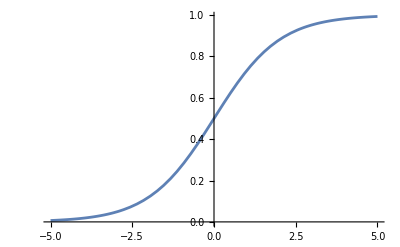

```mathematica
Plot[f[x],{x,-5,5}]
```

```mathematica
fpp[x_] =D[f[x],{x,2}]
```

(2 ⅇ^(-2 x))/((1+ⅇ^-x)^3)-ⅇ^-x/((1+ⅇ^-x)^2)

```mathematica
fpp[x]
```

(2 ⅇ^(-2 x))/((1+ⅇ^-x)^3)-ⅇ^-x/((1+ⅇ^-x)^2)

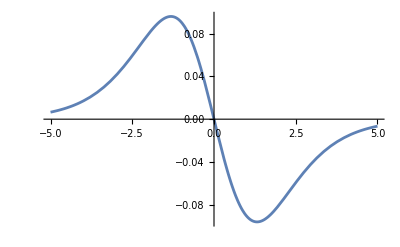

```mathematica
Plot[fpp[x],{x,-5,5}]
```

```mathematica
g[x_] := Sin[2x]
```

```mathematica
D[g[x],{x,2}]
```

-4 Sin[2 x]

-4 Sin[2 x]

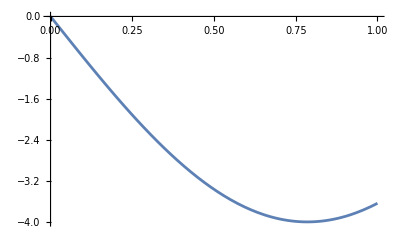

```mathematica
r[x_] = D[g[x],{x,2}]
Plot[r[x],{x,0,1}]
```